```mathematica
nlinhas=15
Rugo[xkezd_,ykezd_,xveg_,yveg_]:={
hx=xveg-xkezd;hy=yveg-ykezd;szel=0.2;veghossz=1.15;
hossz=√(hx^2+hy^2);
dh=(hossz-2*veghossz)/nlinhas;
{xkezd,ykezd}}~Join~{{xkezd+hx*(dh+veghossz)/hossz,ykezd+hy*(dh+veghossz)/hossz}}~Join~Table[If[OddQ[i],{xkezd+hx*(i*dh+veghossz)/hossz+hy*szel/hossz,ykezd+hy*(i*dh+veghossz)/hossz-hx*szel/hossz},
{xkezd+hx*(i*dh+veghossz)/hossz-hy*szel/hossz,ykezd+hy*(i*dh+veghossz)/hossz+hx*szel/hossz}],{i,2,nlinhas-2}]~Join~{{xkezd+hx*((nlinhas-1)*dh+veghossz)/hossz,ykezd+hy*((nlinhas-1)*dh+veghossz)/hossz}}~Join~{{xveg,yveg}}


parabola[pts_]:=Module[{x,func,xmin,xmax},func=Fit[pts,{1,x,x^2},x];
xmin=Min[pts[[All,1]]];
xmax=Max[pts[[All,1]]];
Cases[Plot[func,{x,xmin,xmax}],_Line,-1]]
```

15

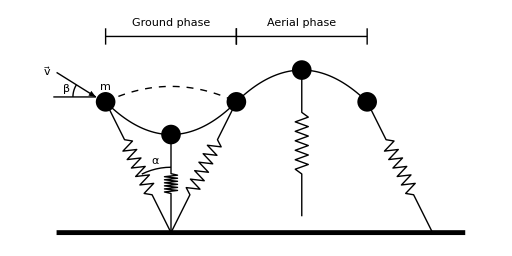

```mathematica
(*pontos da parabola*)
points={{-2,4},{0,3},{2,4}};
points2={{-2,4},{0,√20},{2,4}};
points3={{2,4},{4,√20+0.5},{6,4}};

image1=Graphics[{
Line[Rugo[0,0,-2,4]],
Line[Rugo[0,0,0,3]],
Line[Rugo[0,0,2,4]],
Black,Disk[{-2,4},0.3],
Black,Disk[{0,3},0.3],
Black,Disk[{2,4},0.3],
Black,parabola[points],
Black,Dashed, parabola[points2],
Dashing[None],Arrow[{{-3.5,4.9},{-2.3,4.15}}],
Text["β",{-3.2,4.4}],
Text["m",{-2,4.45}],
Text["α",{ -0.5,2.2}],
Text["v⃗",{-3.8,4.9}],
Circle[{-2.3,4.15},0.7,{π +ArcTan[(4.15-4.9)/(-2.3+3.5)],π}],
Circle[{0,0},2,{π/2,ArcTan[4/-2]+π}],
Line[{{-2.3,4.15},{-3.6,4.15}}],
Line[Rugo[4,0+0.5,4,√20+0.5]],
Black,Disk[{4,√20+0.5},0.3],
Line[Rugo[0+8,0,-2+8,4]],
Black,Disk[{-2+8,4},0.3],
Black,parabola[points3],
AbsoluteThickness[3.5],Line[{{-3.5,0},{9,0}}],
AbsoluteThickness[Medium],Line[{{-2,6},{2,6}}],
Line[{{-2,6.25},{-2,5.75}}],
Line[{{2,6.25},{2,5.75}}],
Text["Ground phase",{0,6.4}],
AbsoluteThickness[Medium],Line[{{2,6},{6,6}}],
Line[{{2,6.25},{2,5.75}}],
Line[{{6,6.25},{6,5.75}}],
Text["Aerial phase",{4,6.4}]

}]
```

```mathematica
SetDirectory["/home/nteixeira/S1_2018_2019/PMEFT/TAFC/desenhos"]
```

/home/nteixeira/Desktop/S1_2018_2019/PMEFT/TAFC/desenhos

```mathematica
Export["Blickhan_model.png",image1,ImageResolution->300]
```

Blickhan_model.png